```mathematica
t = -1./12 0.25{{4, -2}, {-3, 1}};
12. Inverse[IdentityMatrix[2] - t] - 10.IdentityMatrix[2]
```

```mathematica
{{1.1030684500393395,0.4531864673485445},{0.6797797010228168,1.7828481510621579}}
```

{{1.10307,0.453186},{0.67978,1.78285}}

```mathematica
{{1.1030684500393395,0.4531864673485445},{0.6797797010228168,1.7828481510621579}}
```

{{1.10307,0.453186},{0.67978,1.78285}}

```mathematica
{{1.1030684500393395,0.4531864673485445},{0.6797797010228168,1.7828481510621579}}
```

```mathematica
Inverse[IdentityMatrix[2] - t]
```

{{0.925256,0.0377655},{0.0566483,0.981904}}

```mathematica
Inverse[{{0.925255704169945,0.037765538945712045},{0.05664830841856807,0.9819040125885131}}]
```

{{1.08333,-0.0416667},{-0.0625,1.02083}}

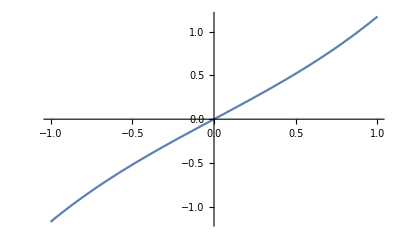

```mathematica
Plot[Sinh[x], {x, -1, 1}]
```

```mathematica
Exp[-I a x]
```

ⅇ^(-ⅈ a x)

```mathematica
ExpToTrig[ⅇ^(-ⅈ a x)]
```

Cos[a x]-ⅈ Sin[a x]

```mathematica
ClearAll["Global`*"]
```

```mathematica
v0 = {{1,2},{3,4}}; 
v1 = {{5,6},{7,8}};
v2 = {{9,10}, {11, 12}};
v3 = {{9.1, 10.1},{11.1, 12.1}};
t[v_]:=-1./12 0.25 (5 IdentityMatrix[2] - v);
u[v_]:=12.Inverse[IdentityMatrix[2] - t[v]] - 10. IdentityMatrix[2];
ep[v_,x_]:=(IdentityMatrix[2]-t[v]).{{Sinh[√(2Abs[5.-v[[1,1]]])x], 0}, {0, Sinh[√(2.Abs[5.-v[[2,2]]])x]}};
em[v_,x_]:=(IdentityMatrix[2]-t[v]).{{Cosh[√(2.Abs[5.-v[[1,1]]])x], 0}, {0, Cosh[√(2.Abs[5.-v[[2,2]]])x]}};
b = IdentityMatrix[2];
R0Inv = Inverse[u[v0]].(IdentityMatrix[2] + b);
R1 = u[v1]-R0Inv;
R2 = u[v2] - Inverse[R1];

s = Inverse[R2.ep[v2, 1] - ep[v3, 1.5]].(R2.em[v2,1]-em[v3, 1.5])
```

```mathematica
{{1.012148643689026,0.005671732038210031},{0.0039020154465922163,1.0011947023937202}}
```

{{1.01215,0.00567173},{0.00390202,1.00119}}

```mathematica
{{1.0104693157826343,0.005191006883148441},{0.006722094551820046,1.0023310970160573}}
```

{{1.01047,0.00519101},{0.00672209,1.00233}}